```mathematica
ClearAll@f;
f[x_]:=((x-49)(x-19))/((x-64)(x+1))
```

```mathematica
Manipulate[Refresh[functions=Table[D[f[x],{x,n}],{n,0,nMax,1}];
orders=Table[D[f[x],{x,n}]//Inactivate//TraditionalForm//ToString,{n,0,nMax,1}];
labels=MapThread[#1<>" = "<>ToString[#2,TraditionalForm]&,{orders,functions}];];
Plot[functions,{x,0,500},PlotLabels->labels,ImageSize->700,AspectRatio->1,PlotLabel->Row[{"f(x) = ",f[x]}]],{{nMax,1,"Order"},1,10,1,PopupMenu}]
```

```mathematica
((x-49)(x-19))/((x-64)(x+1))==1
```

((-49+x) (-19+x))/((-64+x) (1+x))==1

```mathematica
Reduce[((-49+x) (-19+x))/((-64+x) (1+x))==1]
```

x==199

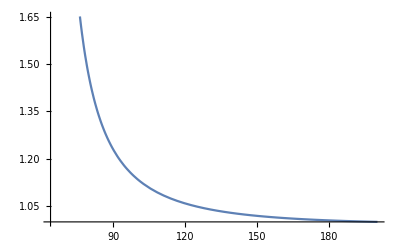

```mathematica
Plot[((-49+x) (-19+x))/((-64+x) (1+x)),{x,64,200}]
```

WolframAlphaQueryResults

((-49+x) (-19+x))/((-64+x) (1+x))>0

```mathematica
((-49+x) (-19+x))/((-64+x) (1+x))>0
```

```mathematica
Reduce[((-49+x) (-19+x))/((-64+x) (1+x))>0]
```

x<-1||19<x<49||x>64

```mathematica
Reduce[((-49+x) (-19+x))/((-64+x) (1+x))>1]
```

x<-1||64<x<199

```mathematica
Reduce[((-49+x) (-19+x))/((-64+x) (1+x))<1]
```

-1<x<64||x>199

WolframAlphaQueryResults

((-49+x) (-19+x))/((-64+x) (1+x))>1

```mathematica
FullSimplify[((-49+x) (-19+x))/((-64+x) (1+x))-1]
```

-(5 (-199+x))/((-64+x) (1+x))